```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
l=ReadList["test1-carry-sigma=1_0-int.dat"];
l=N[l];
len=Length[l]
```

1048576

```mathematica
Mean[l]
StandardDeviation[N@l]
```

0.

1.08023

{1.,0.691383,0.718391,0.696121,0.678995,0.666447,0.656123,0.647482,0.640035,0.633392,0.627448,0.621798,0.616284,0.612462,0.608544,0.604389,0.600592,0.596657,0.593313,0.590277,0.587492}

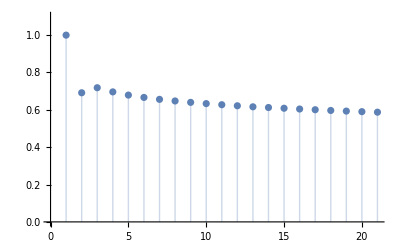

13.6876

```mathematica
cf=CorrelationFunction[l,{20}]
ListPlot[cf,Filling->0,PlotRange->{0,1.1}]
Total[cf]
```